```mathematica
SetDirectory[NotebookDirectory[]];
Get["Packages\\TextbookFigurePreamble.wl"] ;
Get["LatticePhyllotaxis`",Path->FileNameJoin[PersistentSymbol["persistentGitHubPath"],"GeometricalPhyllotaxis\\Mathematica\\Packages"]];
```

## Setup

```mathematica
(*ResourceFunction["matexInstall"][];
*)
(* Needs["PacletManager`"];
PacletInstall["C:\\Users\\jonat\\Downloads\\matex-1.7.10.paclet"];
Configurematex[
"pdfLaTeX"->"C:\\texlive\\2023\\bin\\windows\\pdflatex.exe","Ghostscript"->"C:\\Program Files\\gs\\gs10.04.0\\bin\\gswin64c.exe"
] *)

(*<< matex`
SetOptions[matex,"Preamble"->{"\\usepackage{CormorantGaramond,gillius2}"}];
*)
pvectorName[n_] := Subscript[p, n]
phatvectorName[n_] := Subscript[OverHat[p], n];
paraNumber[n_] := paraNumber[n,0.03];
paraNumber[n_,scale_] := Style[ToString[n],FontFamily->jStyle["FontFamily"],FontSize->Scaled[scale]];

jParastichyColour[n_] := jStyle["ParastichyColour"][n];
jFont[n_] := {FontFamily->jStyle["FontFamily"],FontSize->n};
```

```mathematica
exportFigures := Timing@{
{txbExport[Txb0400SumDifference]
,txbExport[Txb0400Coordinates]
,txbExport[Txb0400Complementary]
,txbExport[Txb0400Periodic]
},
{txbExport[Txb0400Parastichy5]
,txbExport[Txb0400Parastichy45]
,txbExport[Txb0400PPairs]
,txbExport[Txb0400Apextriangle]
},
{txbExport[Txb0400LatticesSpecialD]
,txbExport[Txb0400Spiral ]
,txbExport[Txb0400Reduction]
,txbExport[Txb0400JeanX]
},
{txbExport[Txb0400LowOrder]
,txbExport[Txb0400FibLattices]
,txbExport[Txb0400duBonnet]
,txbExport[Txb0400LatticeTypes]
}
, {txbExport@Txb0400GeneratingIntervals,
txbExport@Txb0400SpiralExample}
}
shExport[x_] := x;
(*shExport[x_] := "Not exported"*)
```

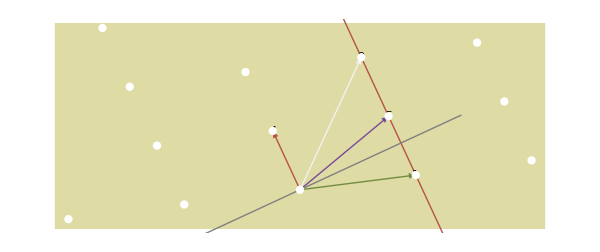
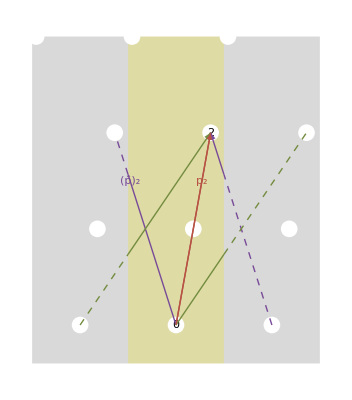
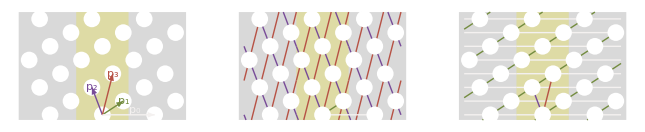
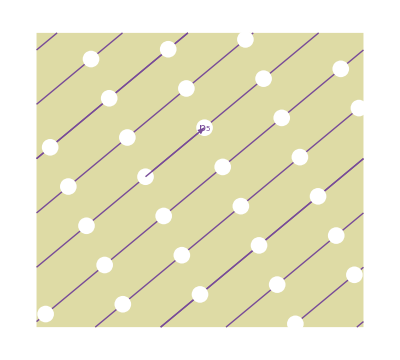
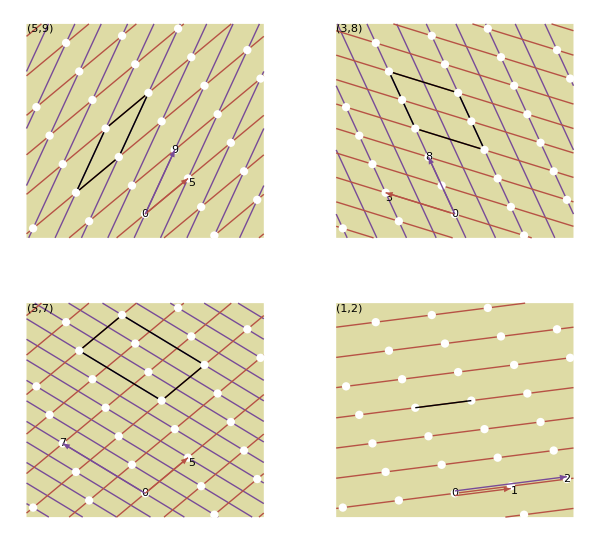
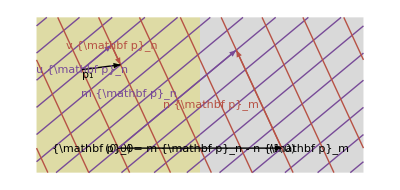
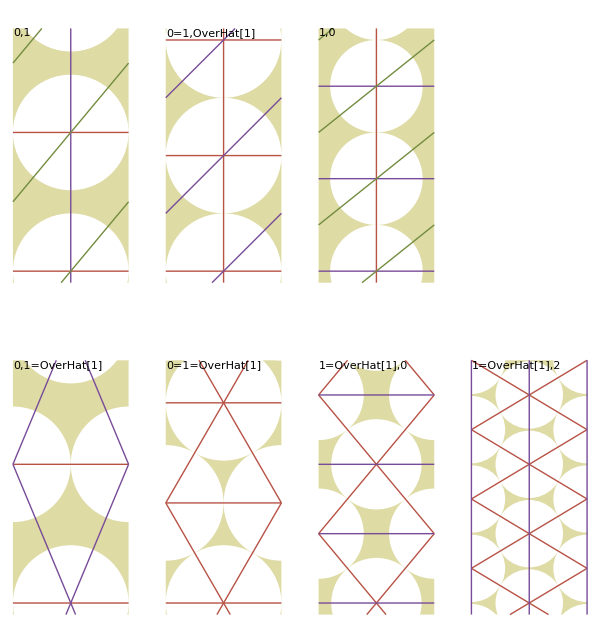
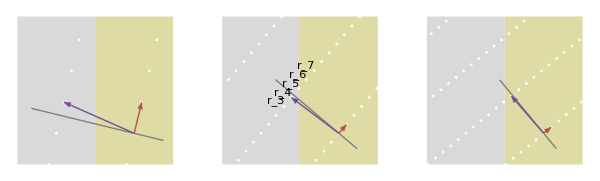
{3.10938,{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics--Graphics--Graphics--Graphics--Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-}}}

```mathematica
exportFigures
```

```mathematica
(*exportFigures*)
```

## Fundamental theorem - figsumdiff

```mathematica
Txb0400SumDifference :=  Module[{},
lattice= latticeCreateDH[{17/72,0.03},{-.08,.34}];
jpt[m_] := latticePoint[lattice,m];
paraNormal[n_] := Module[{x,z},{x,z}=jpt[n]; (z/(x^2+z^2)){-z,x}];
{pp1,pp2,pp3} = latticePrincipal3ParastichyNumbers[lattice];
pp4 = If[pp3==pp1+pp2, Abs[pp2-pp1],pp1+pp2];
Graphics[Style[
{
{jStyle["CylinderColour"],Rectangle@@Transpose[latticeGetCylinder[lattice]]}
,{Thick,jParastichyColour[1],Arrow[{jpt[0],jpt[pp1]}]}
,{Thick,jParastichyColour[2],Arrow[{jpt[0],jpt[pp2]}]}
,{Thin,jParastichyColour[4],Arrow[{jpt[0],jpt[pp4]}]}
,{Thin,jParastichyColour[3],Arrow[{jpt[0],jpt[pp3]}]}
,{Thin,jParastichyColour[1],Line[{jpt[pp2-2 pp1],jpt[pp2+3pp1]}]}
,{Thick, Gray, Line[ {jpt[0]-0.4paraNormal[pp1],jpt[0] +  0.4 paraNormal[pp1]}]}
,{Text[paraNumber[pp1],jpt[pp1],{3,0}]}
,{Text[paraNumber@pp2,jpt[pp2],{-3,0}]}
,{Text[paraNumber@pp4,jpt[pp4],{-3,0}]}
,{Text[paraNumber@pp3,jpt[pp3],{-3,0}]}
,{AbsolutePointSize[6],White, latticeGraphicPoints[lattice]}
}],PlotRange->latticeGetCylinder[lattice]
,ImageSize->600
]
];
```

## Lattice coordinates - figcoord

```mathematica
Txb0400Coordinates:= Module[{lattice,d,h},
{d,h} = {0.4,0.4};
lattice= latticeCreateDH[{d,h},{-.5,1.5}];
jpt[m_] := latticePoint[lattice,m];

cylinder:= {jStyle["CylinderColour"],Rectangle@@Transpose[latticeGetCylinder[lattice]]};
plotrange = {{-1.6,1.6},latticeGetCylinder[lattice][[2]]};
latticep = latticePoints[ lattice];
dashHeight = 2;
dash = Rotate[Line[{{-0.5,dashHeight-.1},{-0.5,dashHeight+.1}}], 30 Degree];
doubledash = {dash,Translate[dash,{0,-.05}]};

dhshowpt =  jpt[2] - {1,0};
pts = {White,Point[latticep],Translate[Point[latticep],{1,0}],Translate[Point[latticep],{-1,0}]};
framerect = {FaceForm[LightGray],EdgeForm[None],Rectangle @@ Transpose@plotrange};
glabel[x_] := Text[x,{plotrange[[1,1]],plotrange[[2,2]]},{-1,1},Background->White];

pointName[n_] := matex["l_"<> ToString[n]];
latexMath[text_,pos_,align_] := Text[matex[text],pos,align];
c2 = Graphics[Style[{
framerect,cylinder
, doubledash, Translate[doubledash,{1,0}]
,{PointSize[.03],pts}
(*, Text["divergence d",dhshowpt,{-0.6,1.2}]
*)
, Text["\\text{{divergence} }d",dhshowpt+{d/2,0},{0,2}]
, Text["\\text{{rise} }h",dhshowpt+{latticeDivergence[lattice],latticeRise[lattice]},{0,-1.2}]
,Arrowheads[.05]
, Arrow[{dhshowpt,dhshowpt+{latticeDivergence[lattice],0}}]
, Arrow[{dhshowpt+{latticeDivergence[lattice],0},dhshowpt+{latticeDivergence[lattice],latticeRise[lattice]}}]
(*, latexMath["(0,0)",jpt[0],{0,-1.4}]
*), latexMath["(d,h)",jpt[1],{0,-1.4}]
, latexMath["(2d-1,2h)",jpt[2],{0,-1.4}]
, latexMath["(2d,2h)",jpt[2]+{1,0},{0,-1.4}]
, latexMath["(3d-1,3h)",jpt[3],{0,-1.4}]
,latexMath["x",{plotrange[[1,2]],0},{1,-1}]
,latexMath["z",{0,plotrange[[2,2]]},{1,1}]
,glabel["a"]
},jFont[12]]
,PlotRange->plotrange
,AspectRatio->Full
,Axes->True
,Ticks->{{-1,-1/2,0,1/2,1},{{h,"h"}}}
,AxesOrigin->{0,0}
,AspectRatio->Full
,BaseStyle->{FontFamily->jStyle["LaTeXDefaultFamily" ]}];
c3 =Graphics[Style[ {
framerect,cylinder
,{PointSize[.03],pts}
, Text[pointName[0],jpt[0],{0,1.4}]
, Text[pointName[1],jpt[1],{0,-1.4}]
, Text[pointName[2],jpt[2],{0,-1.4}]
, Text[pointName[3],jpt[3],{0,-1.4}]
,Arrowheads[.05]
, {Thick,jParastichyColour[1], Arrow[{jpt[0],jpt[1]}]}
, {Thick,jParastichyColour[2], Arrow[{jpt[0],jpt[2]}]}
, {Thick,jParastichyColour[3], Arrow[{jpt[0],jpt[3]}]}
, {Thick,jParastichyColour[4], Arrow[{{0,0},{1,0}}]}
, {jParastichyColour[1],Text[pvectorName[1],jpt[1]/2,{-1.8,0}]}
, {jParastichyColour[2],Text[pvectorName[2],jpt[2]/2,{1.8,0}]}
, {jParastichyColour[3],Text[pvectorName[3],jpt[3]/2,{-1.8,0}]}
, {jParastichyColour[4],Text[pvectorName[0],{1/2,0},{1,-1.4}]}
,glabel["b"]
},jFont[12]],
PlotRange->plotrange,AspectRatio->Full
];

GraphicsRow[{c2,c3},AspectRatio->1,ImageSize->600,Frame->None]
];
```

```mathematica
shExport[Txb0400Coordinates]
```

## Cylindrical and periodic lattices

```mathematica
makec456 := Module[{lattice,jpt,cylinder,latticep,c4,c5,c6,framerect,plotrange},
lattice= latticeCreateDH[{0.4,0.08},{-.03,.6}];
jpt[m_] := latticePoint[lattice,m];
pset[m_] := latticeParastichyLines[lattice,m];

cylinder:= {jStyle["CylinderColour"],Rectangle@@Transpose[latticeGetCylinder[lattice]]};
plotrange = {{-1.6,1.6},latticeGetCylinder[lattice][[2]]};
latticep = latticePoints[ lattice];
(*dashHeight = 2;
dash = Rotate[Line[{{-0.5,dashHeight-.1},{-0.5,dashHeight+.1}}], 30 Degree];
doubledash = {dash,Translate[dash,{0,-.05}]};

dhshowpt = 2;*)
pts = {Point[latticep],Translate[Point[latticep],{1,0}],Translate[Point[latticep],{-1,0}]};
framerect = {FaceForm[LightGray],EdgeForm[None],Rectangle @@ Transpose@plotrange};
glabel[x_] := Text[x,{plotrange[[1,1]],plotrange[[2,2]]},{-1,1},Background->White];


pn[n_] := latticeParastichyNumbers[lattice][[n]];
wps = 0.03;
ar = latticeGetCylinderLU[lattice][[2]]-latticeGetCylinderLU[lattice][[1]];
c4 =Graphics[Style[ {
framerect,cylinder
,{PointSize[wps],White,pts}
,Arrowheads[.04]
, {Thick,jParastichyColour[3], Arrow[{jpt[0],jpt[1]}]}
, {Thick,jParastichyColour[2], Arrow[{jpt[0],jpt[pn[1]]}]}
, {Thick,jParastichyColour[1], Arrow[{jpt[0],jpt[pn[2]]}]}
, {Thick,jParastichyColour[4], Arrow[{{0,0},{1,0}}]}
, {jParastichyColour[4],Text[pvectorName[0],{1/2,0},{-1,-1}]}
, {jParastichyColour[3],Text[pvectorName[1],jpt[1],{0,-1}]}
, {jParastichyColour[2],Text[pvectorName[pn[1]],jpt[pn[1]],{1.8,0}]}
, {jParastichyColour[1],Text[pvectorName[pn[2]],jpt[pn[2]],{-1.8,0}]}
},jFont[Scaled[0.05]]],
PlotRange->plotrange,AspectRatio->ar
];

c5 =Graphics[Style[ {
framerect,cylinder
,{jParastichyColour[2],Map[Translate[pset[ pn[1]],{#,0}]&,{-1,0,1}]}
,{jParastichyColour[1],Map[Translate[pset[ pn[2]],{#,0}]&,{-1,0,1}]}
, {jParastichyColour[3], Line[{jpt[0],jpt[1]}]}
, {jParastichyColour[4], Line[{jpt[0],{1,0}+jpt[0]}]}
,{PointSize[wps],White,pts}
},jFont[Scaled[0.03]]],
PlotRange->plotrange,AspectRatio->ar
];
c6 =Graphics[Style[ {
framerect,cylinder
,{jParastichyColour[4],Map[Translate[pset[ 0],{#,0}]&,{-1,0,1}]}
,{jParastichyColour[3],Map[Translate[pset[ 1],{#,0}]&,{-1,0,1}]}
, {jParastichyColour[2], Line[{jpt[0],jpt[pn[1]]}]}
, {jParastichyColour[1], Line[{jpt[0],jpt[pn[2]]}]}
,{PointSize[wps],White,pts}
},jFont[12]],
PlotRange->plotrange,AspectRatio->ar
];
{c4,c5,c6}
]

Txb0400Periodic:= GraphicsRow[makec456,Frame->None]
```

```mathematica
shExport[Txb0400Periodic]
```

## Complementary vectors figcomplementary

```mathematica
Txb0400Complementary := Module[{lattice,spirh,psize,smidge,jpt,cylinder,cylinderminusone,latticep,latticeminusone,jplus1,gpoint,jminus1,bpoint},
spirh = 3;
psize= PointSize[.03];
lattice= latticeCreateDH[{13/72,1},{-.4,spirh}];
jpt[m_] := latticePoint[lattice,m];
cylinder:= Rectangle@@Transpose[latticeGetCylinder[lattice]];
cylinderminusone = {Translate[cylinder,{-1,0}],Translate[cylinder,{1,0}]};


latticep = latticePoints[ lattice];
latticeminusone = Map[ {#[[1]]-1,#[[2]]} &, latticep];

smidge = 0.00;

jplus1 = jpt[2]+ {1,0};
gpoint = jplus1 * ( 1/2 )/ (jplus1[[1]]);
jminus1 = jpt[2]- {1,0};
bpoint = jminus1 * ( -1/2 )/ (jminus1[[1]]);


Graphics[Style[
{
{jStyle["CylinderColour"],cylinder},{LightGray,cylinderminusone},
,{White,psize,Point[latticep],Point[latticeminusone],Translate[Point[latticep],{1,0}]}
,Text[ paraNumber[0],jpt[0],{0,1.6}]
(*,Text[ paraNumber[1],jpt[1],{-1.6,0}]
*),Text[ paraNumber[2],jpt[2],{0,-1.6}]
,{ jParastichyColour[1],Text[ pvectorName[2],0.75*jpt[2],{1.8,0}]}
,{ jParastichyColour[2],Text[ phatvectorName[2],0.75*(jpt[2]-{1,0}),{-1.8,0}]}
,{Thick,jParastichyColour[1],Arrow[{{0,0},jpt[2]}+{smidge,smidge}]}
,{Thick,jParastichyColour[2],Line[{{0,0},bpoint}]}
,{Thick,jParastichyColour[2],Dashed,Translate[Line[{{0,0},bpoint}],{1,0}]}
,{Thick,jParastichyColour[3],Line[{{0,0},gpoint}]}
,{Thick,jParastichyColour[3],Dashed,Translate[Line[{{0,0},gpoint}],{-1,0}]}
,{Thick,jParastichyColour[3],Translate[Arrow[{gpoint,jplus1}],{-1,0}]}
,{Thick,jParastichyColour[3],Dashed,Translate[Line[{gpoint,jplus1}],{0,0}]}
,{Thick,jParastichyColour[2],Translate[Arrow[{bpoint,jminus1}],{1,0}]}
,{Thick,jParastichyColour[2],Dashed,Translate[Arrow[{bpoint,jminus1}],{0,0}]}
,{Thick,jParastichyColour[1],Arrow[{{0,0},jpt[2]}]}
},jFont[16]],
PlotRange->{{-1.5,1.5},latticeGetCylinder[lattice][[2]]}
]
];
```

```mathematica
shExport[Txb0400Complementary]
```

## Parastichy vector fig17725p

```mathematica
Txb0400Parastichy5 := Module[{lattice,jpt,pset,oset5},
lattice= latticeCreateDH[{17/72,0.03},{-0.1,0.8}];
jpt[m_] := latticePoint[lattice,m];

pset[m_] := latticeParastichyLines[lattice,m];
oset5 = latticeParastichyLines[lattice,5,0];

Graphics[Style[
{
{jStyle["CylinderColour"],latticeGraphicsCylinder[lattice]},
Table[Text[ i,jpt[i],{0,1.4}],{i,0,10}],
,{Thick,jParastichyColour[2],oset5}
,{Thin,jParastichyColour[2],pset[5]}
,{White,PointSize[.03],Point[ latticePoints[ lattice]]}
,{Thick,jParastichyColour[2],Arrow[{jpt[12],jpt[17]}]}
,{jParastichyColour[2],Text[pvectorName[5],jpt[17],{0,2}]}
},jFont[Scaled[0.05]]]]
];
```

```mathematica
shExport[Txb0400Parastichy5]
```

## Parastichy lines fig1772

```mathematica
fig1772[paraList_] :=
Module[{lattice,cylinder,latticep},
lattice= latticeCreateDH[{17/72,0.03},{-0.1,1.2}];
cylinder:= Rectangle@@Transpose[latticeGetCylinder[lattice]];
latticep = latticePoints[ lattice];

jpt[m_] := latticePoint[lattice,m];
plines[m_,n_] := latticeParastichyLines[lattice,m,n];
pset[m_] := latticeParastichyLines[lattice,m];

Graphics[Style[
{
{jStyle["CylinderColour"],latticeGraphicsCylinder[lattice]}
, Map[ {#[[1]],pset[#[[2]]] }&,paraList]
,{PointSize[.03],White,Point[latticep]}
},jFont[16]]
]
];

fig1772P0 := fig1772[{}];
fig1772P4 := fig1772[{{jParastichyColour[1],4}}];
fig1772P5 := fig1772[{{jParastichyColour[2],5}}];
fig1772P9 := fig1772[{{jParastichyColour[3],9}}];
```

```mathematica
{txbExport[fig1772P0],txbExport[fig1772P4],txbExport[fig1772P5],txbExport[fig1772P9]}
```

```mathematica
notate1772[paraList_,doNotation_:True] :=
Module[{lattice,cylinder,latticep},
lattice= latticeCreateDH[{17/72,0.03},{-0.1,1.2}];
cylinder:= Rectangle@@Transpose[latticeGetCylinder[lattice]];
latticep = latticePoints[ lattice];

jpt[m_] := latticePoint[lattice,m];
plines[m_,n_] := latticeParastichyLines[lattice,m,n];
pset[m_] := latticeParastichyLines[lattice,m];
dhshowpt= jpt[25];
Graphics[Style[
{
{jStyle["CylinderColour"],latticeGraphicsCylinder[lattice]}
,If[doNotation,
{
 Arrow[{dhshowpt,dhshowpt+{latticeDivergence[lattice],0}}],
,Table[Text[ i,jpt[i],{0,1.4}],{i,0,10}]
, Text["divergence d",dhshowpt+{latticeDivergence[lattice]/2,0},{0,2}]
,
 Line[{dhshowpt+{latticeDivergence[lattice],0},dhshowpt+{latticeDivergence[lattice],latticeRise[lattice]}}],
,Table[Text[ i,jpt[i],{0,1.4}],{i,0,10}]
, Text["rise h",dhshowpt+{latticeDivergence[lattice],latticeRise[lattice]/2},{-2,0}]
}
]
, Map[ {#[[1]],pset[#[[2]]] }&,paraList]
,{PointSize[.03],White,Point[latticep]}
},jFont[16]]
]
];
```

```mathematica
sheffield1772 := notate1772[{}]
```

```mathematica
txbExport[sheffield1772]
```

```mathematica
(*GraphicsGrid[{{
shExport[fig1772P0],
shExport[fig1772P4],
shExport[fig1772P5],
shExport[fig1772P9]
}}]*)
(* useful for powerpoint *)
```

```mathematica
Txb0400Parastichy45:= Show[fig1772[{{jParastichyColour[1],4},{jParastichyColour[2],5},{jParastichyColour[3],1}}],
Graphics[Style[{
 {Thick,jParastichyColour[1],Arrow[{jpt[0],jpt[4]}]}
, {Thick,jParastichyColour[2],Arrow[{jpt[0],jpt[5]}]}
, {Thick,jParastichyColour[3],Arrow[{jpt[0],jpt[1]}]}
,{jParastichyColour[2],Text["5",jpt[5],{0,2}]}
,{jParastichyColour[1],Text["4",jpt[4],{0,2}]}
,{jParastichyColour[3],Text["1",jpt[1],{0,2}]}
},jFont[16]]
]
]
```

```mathematica
shExport[Txb0400Parastichy45]
```

## Oneonehat bonnet

```mathematica
(*
PersistentSymbol["persistentTextbookFigureDirectory","Local"]="C:\\Users\\jonat\\Documents\\GitHub\\MathematicalPhyllotaxis\\LaTeX\\Figures"
bonnetImage = Import[PersistentSymbol["persistentTextbookFigureDirectory","Local"],"BonnetXXCropThirdOrder.jpg"];
*)
bonnetImage = Import[FileNameJoin[{PersistentSymbol["persistentTextbookFigureDirectory","Local"],"BonnetXXCropThirdOrder.jpg"}]];

Txb0400duBonnet := Module[{lattice,jpt},
lattice= latticeCreateDH[{1/2,0.6},{-0.4,2.2}];
jpt[m_] := latticePoint[lattice,m];
jpt[hat[m_]] := latticePoint[lattice,m,False];
g = Graphics[
{{Style[
{{jStyle["CylinderColour"],latticeGraphicsCylinder[lattice]}
,PointSize[0.03],White,Point[ latticePoints[ lattice]],
{White,Point[latticePoint[lattice,1]-{1,0}],Point[latticePoint[lattice,3]+{1,0}]},
{Thick,jParastichyColour[1],Arrow[{jpt[0],jpt[1]}]},
{jParastichyColour[1],Text[pvectorName[1],(jpt[0]+jpt[1])/2,{-2,0}]},
{jParastichyColour[1],Text[phatvectorName[1],(jpt[0]+jpt[hat[1]])/2,{2,0}]},
{Thick,jParastichyColour[1],Arrow[{jpt[0],jpt[hat[1]]}]}
},jFont[Scaled[0.03]]]
}
,{Inset[bonnetImage,{0.8,-0.4},{Left,Bottom},{Automatic,2.6}]}
},
PlotRange->{{-1,2},{-0.5,2.5}},Axes->False
]
];
```

Import::chtype: First argument FileNameJoin[{Missing[Nonexistent,PersistentObject[persistentTextbookFigureDirectory,Local]],BonnetXXCropThirdOrder.jpg}] is not a valid file, directory, or URL specification.

```mathematica
shExport[Txb0400duBonnet]
```

## Parastichy pairs figplinesex

```mathematica
Txb0400PPairs := Module[{lattice},
lattice= latticeCreateDH[{17/72,0.03},{-0.1,0.8}];
jpt[m_] := latticePoint[lattice,m];

cylinder := {jStyle["CylinderColour"],Rectangle[{-.5,cylinderLU[[1]]},{0.5,cylinderLU[[2]]}]};

(*pgram[m_,n_,through_] := parallelogram[{h,d},m,n,through];
*)
pset[m_] := latticeParastichyLines[lattice,m];
jpt[m_] := latticePoint[lattice,m];
plines[m_,n_] := latticeParastichyLines[lattice,m,n];


figplinesex057[m0_,m5_,m7_,through_] := Graphics[Style[
{
{jStyle["CylinderColour"],latticeGraphicsCylinder[lattice]}
,{Thin,jParastichyColour[2],pset[m7]},{Thin,jParastichyColour[1],pset[m5]}
,{Thick,Black,Line[latticeParallelogram[lattice,m5,m7,through]]}
,{White,AbsolutePointSize[6],Point[latticePoints[lattice]]}
,Text[ ToString[m0],jpt[m0],{0,1.4}],
Text[ ToString[m5],jpt[m5],{-1,1.4}],
Text[ ToString[m7],jpt[m7],{0,-1.4}],
{Thick,jParastichyColour[1],Arrow[ {jpt[m0],jpt[m5]}]},
{Thick,jParastichyColour[2],Arrow[ {jpt[m0],jpt[m7]}]}
,
Style[Text[StringTemplate["(``,``)"][m5,m7], latticeLabelPosition[lattice],{-1,1},Background->White],FontSize->12]
},jFont[12]
]];

figplinesex57 = figplinesex057[0,5,7,13];
figplinesex38 = figplinesex057[0,3,8,9];
figplinesex59 =  figplinesex057[0,5,9,3];
figplinesex12:= Graphics[Style[
{
{jStyle["CylinderColour"],latticeGraphicsCylinder[lattice]},
{Thin,jParastichyColour[1],pset[1]},
{White,AbsolutePointSize[6],Point[latticePoints[lattice]]},
Text[ "0",jpt[0],{0,1.4}],
Text[ "1",jpt[1],{-1,1.4}],
Text[ "2",jpt[2],{0,1.4}],
{Thick,jParastichyColour[1],Translate[Arrow[ {jpt[0],jpt[1]}],{ 0,-.01}]},
{Thick,jParastichyColour[2],Translate[Arrow[ {jpt[0],jpt[2]}],{0,.01}]},
{Thick,Black,Line[{jpt[12],jpt[13]}]},
Style[Text[StringTemplate["(``,``)"][1,2], latticeLabelPosition[lattice],{-1,1},Background->White],FontSize->12]
},jFont[12]
]];
GraphicsGrid[{{figplinesex59,figplinesex38},{figplinesex57,figplinesex12}},ImageSize->600]
];
```

```mathematica
shExport[Txb0400PPairs]
```

## apextriangle

```mathematica
Txb0400Apextriangle := Block[{m,n,u,v},
lattice= latticeCreateDH[{17/72,0.03},{-0.15,0.8}];
jpt[m_] := latticePoint[lattice,m];
pset[m_] := latticeParastichyLines[lattice,m];
plines[m_,n_] := latticeParastichyLines[lattice,m,n];


pale = Background->Directive[Opacity[0.5],White];
pBox[str_,n_] := DisplayForm[RowBox[{str,pvectorName[n]}]];

Graphics[Style[
{
{jStyle["CylinderColour"],latticeGraphicsCylinder[lattice],
LightGray, Translate[latticeGraphicsCylinder[lattice],{1,0}]}
,
Text[ "(0,0)",jpt[0],{0,1.4},pale],
Text[ "(1,0)",{1,0},{0,1.4},pale],
apexpt = 4* jpt[5];
bpt = 4* jpt[4];
{Thin,jParastichyColour[2],pset[5],Translate[pset[5],{1,0}]},
{Thin,jParastichyColour[1],pset[4],Translate[pset[4],{1,0}]}
,Arrowheads[0.02]
,{Thick,Black,Arrow[ {{0,0},{1,0}}]},
{Thick,jParastichyColour[2],Arrow[ {{0,0},apexpt}]},
{Thick,jParastichyColour[2],Arrow[ {bpt,bpt+jpt[5]}]},
{Thick,jParastichyColour[1],Arrow[ {bpt+jpt[5],bpt+jpt[5]-jpt[4]}]},
{Thick,jParastichyColour[1],Arrow[ {{1,0},apexpt}]},
{Thick,Black,Arrow[ {bpt,bpt+jpt[1]}]},
{jParastichyColour[2],Text[matex["u {\\mathbf p}_n"], bpt,{0,-3},pale]},
,{jParastichyColour[1],Text[matex["v {\\mathbf p}_n"],bpt+jpt[5],{-1.5,0},pale]}
,{Black,Text[ pvectorName[1], bpt,{-3,1},pale]}
,{jParastichyColour[1],Text[matex["n {\\mathbf p}_m"],4*jpt[5]-2.5*jpt[4],{1,1},pale]}
,{jParastichyColour[2],Text[matex["m {\\mathbf p}_n"],2*jpt[5],{1.5,-0.5},pale]}
,{Black,
Text[matex ["{\\mathbf p}_0= m {\\mathbf p}_n - n {\\mathbf p}_m"]
,{0.5,0},{0,1.2}
,pale]}
},jFont[12]],AspectRatio->Automatic
]
];
```

```mathematica
shExport[Txb0400Apextriangle]
```

## Generating interval plot

```mathematica
gLine[{m_,n_}] := gLine[{m,n,Missing[]}];
gLine[{m_,n_,hattedn__}] := Module[{gI,cI,bheight,gIrect,gIo,gIorect,u,v,umnv,umnvLines,res,iLine,Delta},
bheight = 0.1;
gI = If[MissingQ[hattedn],
generatingInterval[{m,n}],If[n==1,Interval[{0,1/2}], Interval[0,1/(2n)]
]
];
gIo = If[MissingQ[hattedn],
generatingOpposedInterval[{m,n}],If[n==1,Interval[{0,1/2}], Interval[0,1/(2n)]
]
];

gIrect  = {EdgeForm[None],FaceForm[LightGray],Rectangle[ {Min@gI,-bheight},{Max@gI,bheight}]};
gIorect  = {EdgeForm[None],FaceForm[jParastichyColour[1]],Rectangle[ {Min@gIo,-bheight},{Max@gIo,bheight}]};

iStyle =  euclideanDelta[{m,n}]<0;

iLine = {Thin,If[ iStyle,Dotted,Dashed],Line[ {{0,0},{1/2,0}}]};

tlabel = If[MissingQ[hattedn],StringTemplate["``,``"][m,n],StringTemplate["``,``"][m,hattedn]];


	res =
{
iLine
, gIrect
,gIorect 
,{Thin,Line[{{0,-bheight},{0,bheight}}],Line[{{1/2,-bheight},{1/2,bheight}}]}
, Text[ tlabel,{.55,0},{0,0}]
}
;
res];
```

```mathematica
(* reconsider with hats *)
```

```mathematica
Txb0400GeneratingIntervals := Graphics[Style[
{
MapIndexed[ Translate[gLine@  #1,{0,-First@#2}]&,{ {1,1},{1,2,"\!\(\*OverscriptBox[\(2\), \(^\)]\)"},{1,2},{2,3},{3,5},{5,8},{8,13},{13,21},{21,34},{1,3,"\!\(\*OverscriptBox[\(3\), \(^\)]\)"},{1,3},{3,4},{4,7},{7,11},{11,18},{18,29}}],
Line[{{0,0},{1/2,0}}]
,Text["0",{0,0},{-1,-1}]
,Text["\\text{divergence }d",{1/4,0},{0,-1}]
,Text["1/2",{1/2,0},{0,-1}]
},
jFont[Scaled[0.05]]],
AspectRatio->1.5,PlotRange->{{0,.65},Automatic}];
```

```mathematica
shExport[Txb0400GeneratingIntervals]
```

## Special pairs Txb0400LatticesSpecialD

```mathematica
Txb0400ShowParastichyLines[h_,d_,cylinderLU_,showCircle_:True]  :=  Module[{latticep,pp,jpt,plines,pset,para1Set,para2Set},
lattice = latticeCreateDH[{d,h},cylinderLU];
ll =latticeLabel[lattice];
llines = Map[latticeParastichyLines[lattice,#]&,ll,{2}];
paraset = MapIndexed[{jParastichyColour[First[#2]],#1}&,llines];

latticePointSize = If[showCircle,Large,Small];

Graphics[{
{jStyle["CylinderColour"],latticeGraphicsCylinder[lattice]}
,If[showCircle,{FaceForm[White],latticeCircles[lattice]/. Circle->Disk},Nothing[]],
, paraset
,If[showCircle,{PointSize[latticePointSize],Point[latticePoints[lattice]]},Nothing[]];
Style[Text[latticeLabelText[lattice],latticeLabelPosition[lattice],{-1,1},Background->White],jFont[Scaled[0.1]]]
},PlotRange->latticeGraphicsPlotRange[lattice]
]
];
```

```mathematica
Txb0400LatticesSpecialD := Module[{},
sPL[{h_,d_},label_] := Show[{
Txb0400ShowParastichyLines[h,d, {-0.1,2.1},True]
}];
GraphicsGrid[{{
(* label ignored and calculated direct *) 
sPL[{1.2,0},"(0,1)"],
sPL[{1,0},"(0=1,\!\(\*OverscriptBox[\(1\), \(^\)]\))"],
sPL[{0.8,0},"(1,0)"]
},{
sPL[{1.2,1/2},"(0,1=\!\(\*OverscriptBox[\(1\), \(^\)]\))"],
sPL[{Sqrt[3]/2,1/2},"(0=1=\!\(\*OverscriptBox[\(1\), \(^\)]\))"],
sPL[{0.6,1/2},"(1=\!\(\*OverscriptBox[\(1\), \(^\)]\),0)"],
sPL[{0.3,1/2},"(1=\!\(\*OverscriptBox[\(1\), \(^\)]\),2)"]
}
},ImageSize->600]
];
```

```mathematica
shExport[Txb0400LatticesSpecialD]
```

## Spiral lattices Txb0400spiral

```mathematica
matex[x_]:=x;
```

```mathematica
Txb0400Spiral := Module[{spirh,psize},
spirh = 1.5;
psize= AbsolutePointSize[2];
cylinderLU = {-.4,spirh};  

dospiral[{h_,d_},rList_] := Module[{nslope,pv,spiral,s1,s2,s3},
lattice = latticeCreateDH[{d,h},cylinderLU];
nslope[1] := (h/(h^2+d^2)){-h,d};
pv = Map[ latticeParastichyVectors[lattice],latticePrincipalParastichyPair[lattice]];

rPoints  =Association@Map[#->latticePoint[lattice,#]&,rList];
rText  =KeyValueMap[
Text[matex["r_" ~~ToString[#1]],If[#2[[1]]>0,#2-{1,0},#2],{1,-.5}]&,rPoints];
spiral = 
Graphics[Style[
{
{jStyle["CylinderColour"],latticeGraphicsCylinder[lattice],
LightGray,Translate[latticeGraphicsCylinder[lattice],{-1,0}]}
,{White,psize,Point[latticePoints[lattice]],
Translate[Point[latticePoints[lattice]],{-1,0}]}
,{Thin, Gray,Line[{1.4*nslope[1],-0.4  * nslope[1]}]}
,{Thick,jParastichyColour[1],Arrow[{{0,0},pv[[1]]}]},
,{Thick,jParastichyColour[2],Arrow[{{0,0},pv[[2]]}]}
,{Black,rText}
},jFont[Scaled[.04]]
],AspectRatio->Automatic];

spiral
];

s1 = dospiral[{0.08,7/72},{}];
s2 = dospiral[{ .115, 7/72},{3,4,5,6,7}];
s3 = dospiral[{ 0.4, 7/72},{}];
GraphicsGrid[ {{s3,s2,s1}},ImageSize->600]
];
```

```mathematica
shExport@Txb0400Spiral
```

## Ordinary pairs not currently used

```mathematica
cylinderLU = {-0.1,2.1};
cylinder2 =  {-0.1,0.2};
dOrdinary = N[17/72];

soPL[{h_,d_},cyl_,showCircle_:True] := Txb0400ShowParastichyLines[h,d,cyl,showCircle];

figordinaryA := GraphicsGrid[{{
soPL[{1.2,dOrdinary},cylinderLU,True]
,soPL[{0.8,dOrdinary},cylinderLU,True]
,soPL[{0.6,dOrdinary},cylinderLU,True]
,soPL[{0.3,dOrdinary},cylinderLU,True]
},{
soPL[{0.15,dOrdinary},cylinderLU,True]
,soPL[{0.1,dOrdinary},cylinderLU,True]
,soPL[{0.05,dOrdinary},cylinderLU,True]
,soPL[{0.025,dOrdinary},cylinderLU,True]
}
},ImageSize->600];
```

```mathematica
Bshow= True;
figordinaryB := GraphicsGrid[{
{
 soPL[{0.025,dOrdinary},cylinder2,Bshow]
,soPL[{0.015,dOrdinary},cylinder2,Bshow]
,soPL[{0.01,dOrdinary},cylinder2,Bshow]

},{
soPL[{0.005,dOrdinary},cylinder2,Bshow]
,soPL[{0.002,dOrdinary},cylinder2,Bshow]
,soPL[{0.001,dOrdinary},cylinder2,Bshow]
}
},ImageSize->600];
```

## Reduction figreduction

```mathematica
Txb0400Reduction := Module[{smidge=0.01,spirh,h,d,lattice,jpt,nslope},
spirh = .5;h = .03;d = 17/72;cylinderLU = {-0.1,spirh};  
lattice = latticeCreateDH[{d,h},cylinderLU];

jpt[m_] := latticePoint[lattice,m];

nslope[5] = { - jpt[5][[2]],jpt[5][[1]] };

Graphics[
Style[
{
{jStyle["CylinderColour"],latticeGraphicsCylinder[lattice]},
Arrowheads[jStyle["ArrowheadSpec"]]
,{White,Point@latticePoints[lattice]}
, { jParastichyColour[1],Text[ pvectorName[5],jpt[5],{-2,0}]}
,{ jParastichyColour[2],Text[ pvectorName[14],jpt[14],{1,-1.5}]}
,{ jParastichyColour[3],Text[ pvectorName[4],jpt[12],{1,-1.5}]}
,{jParastichyColour[1],Translate[Arrow[{{0,0},jpt[5]}],{0,0}]}
,{jParastichyColour[2],Translate[Arrow[{{0,0},jpt[14]}],{0,0}]}
,{jParastichyColour[3],Translate[Arrow[{jpt[8],jpt[12]}],{0,0}]}
,{Thick,Black,Translate[Arrow[{{0,0},jpt[9]}],{0,0}]}
,{Thick,Black,Translate[Arrow[{{0,0},jpt[9]}],{0,0}]}
,{Thick,Black,Translate[Arrow[{{0,0},jpt[4]}],{0,0}]}
,{Thick,Black,Translate[Arrow[{{0,0},jpt[-1]}],{0,0}]}
,{
FaceForm[None],EdgeForm[Black],
Translate[Rotate[Scale[Rectangle[],0.02,{0,0}],ArcTan@@nslope[5]+π/2,{0,0}],nslope[5]*0.55]
}
,{Thin,Dashed,Black,Line[{ nslope[5]*-1.2,nslope[5]*0.7}]}
,{Thin,Dashed,Red,Line[{ jpt[-6],jpt[19]}]}
,Text[matex["{\\mathbf p}_{14}- {\\mathbf p}_5"],jpt[9],{1,-1.5}]
,Text[matex["{\\mathbf p}_{14}- 2{\\mathbf p}_5"],jpt[4],{1,-1.5},Background->jStyle["CylinderColour"]]
,Text[Text[matex["{\\mathbf p}_{14}- 3{\\mathbf p}_5"]],jpt[-1],{1,-1.5}]
}
,jFont[Scaled[0.03]]],
PlotRange->latticeGraphicsPlotRange[lattice]
]
];
```

```mathematica
shExport[Txb0400Reduction]
```

## Jean figcounterx

```mathematica
Txb0400JeanX := Graphics@Module[{smidge,h,d,spirh,cylinderLU,lattice,jpt,pLine},
h = .1;d = 7/72;spirh = .5;
cylinderLU = {-0.1 * spirh ,spirh};  
lattice = latticeCreateDH[{d,h},cylinderLU];
jpt[m_] := latticePoint[lattice,m];
smidge = 0.02;
pLine = latticeParastichyLines[lattice,1];
pLine = {pLine,Translate[pLine,{-1,0}]};

spiral = 
Graphics[Style[
{
Arrowheads[.02],
{jStyle["CylinderColour"],latticeGraphicsCylinder[lattice]},
{LightGray,Translate[latticeGraphicsCylinder[lattice],{-1,0}]}
,{Thin,Red,pLine}
,{
{White,Point[latticePoints[lattice]],
Translate[Point[latticePoints[lattice]],{-1,0}]}}
,Text[ "0",jpt[0],{0,1.4}]
,{ jParastichyColour[2],Text[ pvectorName[2],jpt[2],{2,0}]}
,{ jParastichyColour[1],Text[ pvectorName[1],jpt[1],{2,0}]}
,{ jParastichyColour[2],Text[ phatvectorName[2],jpt[2]-{1,0},{2,0}]}
,Translate[{Thick,jParastichyColour[2],Arrow[{{0,0},jpt[2]}]},{smidge,0}]
,Translate[{Thick,jParastichyColour[1],Arrow[{{0,0},jpt[1]}]},{-smidge,0}]
,{Thick,jParastichyColour[2],Dashed,Arrow[{{0,0},jpt[2]- {1,0}}]}
},jFont[16]],AspectRatio->Automatic
];
spiral
];
```

```mathematica
shExport[Txb0400JeanX]
```

## Lattices organised by length Txb0400LatticeTypes

```mathematica
showLatticeParastichyLines[lattice_,showCircle_:True]  :=  Module[{latticep,pp,jpt,plines,pset,para1Set,para2Set},
ll = latticeLabel[lattice];
llines = Map[latticeParastichyLines[lattice,#]&,ll,{2}];
arrows = MapIndexed[{ jParastichyColour@First[#2],Arrow[{latticePoint[lattice,0],latticeVector[lattice,#1]}]}&,ll,{2}];paraset = MapIndexed[{jParastichyColour[First[#2]],#1}&,llines];paraset ={LightGray,llines};latticePointSize = If[showCircle,Large,Small];latticeP= latticeSetCylinderLU[lattice,{-0.4,0.8}];

Graphics[{
{jStyle["CylinderColour"],latticeGraphicsCylinder[lattice]}
,If[showCircle,{FaceForm[White],latticeCircles[latticeP]/. Circle->Disk},Nothing[]],
,{Thin, paraset}
,{Thick,arrows}
,If[showCircle,{PointSize[latticePointSize],Point[latticePoints[lattice]]},Nothing[]],
Style[Text[latticeLabelText[lattice],latticeLabelPosition[lattice],{-1,1},Background->White],jFont[16]]
},PlotRange->latticeGraphicsPlotRange[lattice]
]
];

figShowHex25 := showLatticeParastichyLines[latticeHexagonal[{2,5},{-0.2,0.6}]];
figShowTC25 := showLatticeParastichyLines[latticeTouchingCircle[{2,5},{-0.2,0.6}]];
figShowMN23 := showLatticeParastichyLines[latticeWithMN[{2,3},{-0.2,0.6}]];
figShowMN25 := showLatticeParastichyLines[latticeWithMN[{2,5},{-0.2,0.6}]];

(* viTouchingCircleBranch[{2,3}] *)
b[theta_] := {1/5,0} + (1/5) * {Cos[theta],Sin[theta]}
```

```mathematica
figShowNoli25 := Module[{},
{nolic,nolir,nolia} = List@@vanItersonTouchingCirclePrimaryNonOpposed[{2,5}];
nolim = Mean[nolia];
dhNoli = nolic + nolir * {Cos[nolim],Sin[nolim]};
(Off[Greater::meprec];Off[LessEqual::meprec];
showLatticeParastichyLines[latticeCreateDH[dhNoli,{-0.2,0.6}]])
];
(* touching circle oddness *)

Txb0400LatticeTypes  := GraphicsGrid[{{figShowMN25,figShowNoli25},{figShowTC25,figShowHex25}}]
```

```mathematica
shExport[Txb0400LatticeTypes]
```

```mathematica
OxOppo := Module[{},
{oppo41 =showLatticeParastichyLines[
latticeCreateDH[latticeDHNonOpposedTC[{1,4}],{-0.2,0.8}]]
,
nonOppo41 =showLatticeParastichyLines[
latticeCreateDH[{0.24,0.06},{-0.2,0.8}]
]
};
GraphicsRow[{nonOppo41,oppo41}]
];
```

```mathematica
txbExport[OxOppo]
```

```mathematica
CamOppo := Module[{},
{oppo41 =showCamLatticeParastichyLines[
latticeCreateDH[latticeDHNonOpposedTC[{1,4}],{-0.2,0.8}]]
,
nonOppo41 =showCamLatticeParastichyLines[
latticeCreateDH[{0.24,0.06},{-0.2,0.8}]
]
};
GraphicsRow[{nonOppo41,oppo41}]
];
```

```mathematica
showCamLatticeParastichyLines[lattice_,showCircle_:True]  :=  Module[{latticep,pp,jpt,plines,pset,para1Set,para2Set},
ll = Echo@latticeLabel[lattice];
ll= {{1,4}};
llines = Map[latticeParastichyLines[lattice,#]&,ll,{2}];
arrows = MapIndexed[
{ jParastichyColour@First[#2],
Arrow[{latticePoint[lattice,0],latticeVector[lattice,#1]}]}&,ll,{2}];

paraset = MapIndexed[{jParastichyColour[First[#2]],#1}&,llines];
paraset ={LightGray,llines};
latticePointSize = If[showCircle,Large,Small];

latticeP= latticeSetCylinderLU[lattice,{-0.4,0.8}];

Graphics[{
{jStyle["CylinderColour"],latticeGraphicsCylinder[lattice]}
,If[showCircle,{FaceForm[White],latticeCircles[latticeP]/. Circle->Disk},Nothing[]],
,{Thin, paraset}
,{Thick,arrows}
,If[showCircle,{PointSize[latticePointSize],Point[latticePoints[lattice]]},Nothing[]]
(*,Style[Text[latticeLabelText[lattice],latticeLabelPosition[lattice],{-1,1},Background->White],jFont[16]]
*)
},PlotRange->latticeGraphicsPlotRange[lattice]
]
];
```

## Txb0400loworder

```mathematica
Txb0400ShowLattice[lattice_]  :=  Module[{ll,llines,paraset,g},

ll = latticeLabel[lattice];
llines = Map[latticeParastichyLines[lattice,#]&,ll,{2}];
paraset = MapIndexed[{jParastichyColour[First[#2]],#1}&,llines];

g=Graphics[{
{jStyle["CylinderColour"],latticeGraphicsCylinder[lattice]}
,
{FaceForm[White],EdgeForm[None],latticeCircles[lattice] /. Circle->Disk},
paraset
,Style[Text[latticeLabelText[lattice],latticeLabelPosition[lattice],{-1,1},Background->White],jFont[16]]
(*,{Point[lattice]}
*)},PlotRange->latticeGraphicsPlotRange[lattice]
];
g
];
```

```mathematica
Txb0400LowOrder := Module[{},
	cylinderLU = {0,1.2};
	p0e1e1 = latticeHexagonal[{0,1},cylinderLU];
	p2e1 = latticeOrthogonal[{1,1},cylinderLU];
	g1 = Txb0400ShowLattice/@{p0e1e1,p2e1};
cylinderLU = {0,0.8};
p1e1 = latticeTouchingCircle[{1,1},cylinderLU];
p1e2= latticeOrthogonal[{1,2},cylinderLU];
p1e2e3 = latticeHexagonal[{1,2},cylinderLU];
g2 = Txb0400ShowLattice/@{p1e1,p1e2,p1e2e3};
cylinderLU = {0,.6};
p2e3 = latticeOrthogonal[{2,3},cylinderLU];
p2e3e5 = latticeHexagonal[{2,3},cylinderLU];
p3e5= latticeOrthogonal[{3,5},cylinderLU];
p3e5e8 = latticeHexagonal[{3,5},cylinderLU];
g3 = Txb0400ShowLattice/@{p2e3,p2e3e5,p3e5,p3e5e8};
cylinderLU = {0,.4};
p3e8 = latticeOrthogonal[{3,8},cylinderLU];
p5e8e13 = latticeHexagonal[{5,8},cylinderLU];
cylinderLU = {0,.8};
p1e3 = latticeHexagonal[{1,3},cylinderLU];
p1e3o = latticeOrthogonal[{1,3},cylinderLU];
g4 = Txb0400ShowLattice/@{p3e8,p5e8e13,p1e3,p1e3o};
cylinderLU = {0,.6};
	p1e3e4 = latticeTouchingCircle[{1,3},cylinderLU];
p3e4  = latticeOrthogonal[{3,4},cylinderLU];
p1e5 = latticeTouchingCircle[{3,4},cylinderLU];
p2e5 = latticeTouchingCircle[{2,5},cylinderLU];
g5 =Txb0400ShowLattice/@{p1e3e4,p3e4,p1e5,p2e5};
g = figLowOrder = Row[{Column[g1],Column[g2],Column[g3],Column[g4],Column[g5]},Spacer[1],Frame->False,Alignment->Center];
g
];
```

```mathematica
shExport[Txb0400LowOrder]
```

## Fibonacci lattices Txb0400FibLattice

```mathematica
showFibParastichyLines[lattice_,showCircle_:True]  :=  Module[{latticep,pp,jpt,plines,pset,para1Set,para2Set},
ll = latticeLabel[lattice];
aline[ix_] := { jParastichyColour[ix],
Line[{latticePoint[lattice,0],latticeVector[lattice,First@ll[[ix]]]}]};
arrows = Table[{aline[ix],Dashed,Translate[aline[ix],{-1,0}]},{ix,Length[ll]}];
labels = MapIndexed[
Style[
Text[#1,latticeVector[lattice,#1],If[#1===1,Offset[{0,-1}],Offset[{0,0}]],Background->jStyle["CylinderColour"]] ,
jParastichyColour@First[#2],jFont[12]
]&,
ll,{2}];
latticePointSize = If[showCircle,Large,Small];
labels = Style[Text[latticeLabelText[lattice],latticeLabelPosition[lattice],{-1,1},Background->White],jFont[16]];
Graphics[{
{jStyle["CylinderColour"],latticeGraphicsCylinder[lattice]}
,{Thick,arrows}
,{PointSize[Medium],White,Point[latticePoints[lattice]]}
,labels
(*,{PointSize[Medium],Black,Point[latticePoint[lattice,1]]}
*)},PlotRange->latticeGraphicsPlotRange[lattice],
ImageSize->150
]
];
f[h_] := showFibParastichyLines[latticeCreateDH[{GoldenRatio-1,h},{-0.01,
If[h>= 0.2,1.45,0.45]}]];
Txb0400FibLattices := Grid[Map[f,{{1,0.5,0.2},{0.15,0.1,0.05},{0.04,0.025,0.015}},{2}]
];
```

```mathematica
frameFibParastichyLines[lattice_,showCircle_:True]  :=  Module[{ll,aline,arrows,labels,latticePointSize},
ll = latticeLabel[lattice];
aline[ix_] := { jParastichyColour[ix],
Line[{latticePoint[lattice,0],latticeVector[lattice,First@ll[[ix]]]}]};
arrows = Table[{aline[ix],Dashed,Translate[aline[ix],{-1,0}]},{ix,Length[ll]}];

latticePointSize = If[showCircle,Large,Small];
labels = Style[Text[latticeLabelText[lattice],latticeLabelPosition[lattice],{-1,1},Background->White],jFont[16]];
Graphics[{
{jStyle["CylinderColour"],latticeGraphicsCylinder[lattice]}
,{Thick,arrows}
,{PointSize[Medium],White,Point[latticePoints[lattice]]}
,labels
(*,{PointSize[Medium],Black,Point[latticePoint[lattice,1]]}
*)},PlotRange->latticeGraphicsPlotRange[lattice],
ImageSize->300
]
];
sToh[s_] := Module[{t}, t= If[s<1/2,2s,2-2 s ];Exp[  ( t+1/2) Log [0.015]]];
frameFib[s_,seconds_] := frameFibParastichyLines[
latticeCreateDH[{GoldenRatio-1, sToh[s/seconds]},{-0.01,1.45}]];
sheffieldFibShow := Module[{vf},
vf = VideoGenerator[frameFib[#,10]&,10];
CopyFile[FindFile@Information[vf,"ResourcePath"]
,"SheffieldFib.mp4",OverwriteTarget->True]
];
```

```mathematica
(*
sheffieldFibShow
*)
```

## Spiral for question

```mathematica
(* relies on Ch3 for lattice plotting, and Ch 4 for van Iterson tree under old numbering,
probalby fig goes in exercises to chapter 3 *)
```

## Tree near spirals

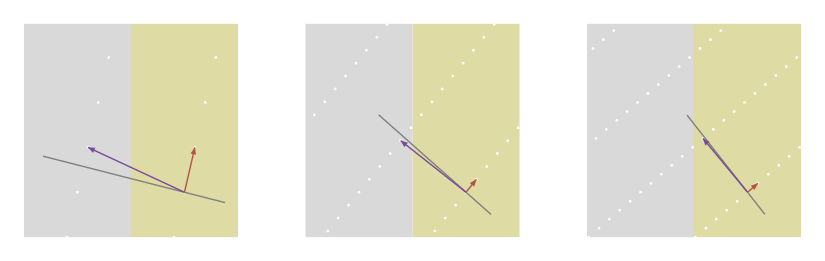

```mathematica
spiralTreePlot[mnPairs_,labelPairs_,opts:OptionsPattern[]] := Module[{regionLabel,prunedTree},
regionLabel[mn_] := panelLabel[mn,viiLabelPoint[mn],0.15];

prunedTree = {
Map[{jParastichyColour[1],viiPrimarySegment[#]}&,mnPairs]
,{LightGray,Map[viiNonPrimarySegments,mnPairs]}
 };


Graphics[
{
 prunedTree
,Map[regionLabel,labelPairs]
},
Evaluate[FilterRules[{opts}, Options[Graphics]]]
]
];

spiralBackground =  Module[{mnPairs,labelPairs,tplaces,ticks},
mnPairs = Join[Nest[addSubTree,{{1,2}},6],{{0,1}}];
labelPairs = Join[Nest[addSubTree,{{1,0}},3],{{1,4}},{}];

spiralRegions = Map[colourSpiral,{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7}}];
Show[
Graphics@spiralRegions,
spiralTreePlot[ mnPairs,{},PlotRange->
{{0.,1/2},{0,0.5}}
,Axes->True,Ticks->{{0,1/2},{0,1/2}},
AxesLabel->{"d","h"}
,PlotRangeClipping->True
 ,BaseStyle->  {FontFamily->  figureStyle["FontFamily"]}
]
]
];

hatTransition[n_] := {Red,Circle[{  1/(2 n+1),0},1/(2 n+1)]}
hdofTransition[d_,n_]:= {d,Module[{z=1/(2n+1)}, Sqrt[ z^2- (d- z)^2]]};
```

Join::heads: Heads addSubTree and List at positions 1 and 2 are expected to be the same.

RegionIntersection::reg: viiPolygon[{1,1},Ordered,Plus] is not a correctly specified region.

RegionIntersection::reg: viiPolygon[{1,1},Ordered,Minus] is not a correctly specified region.

RegionIntersection::reg: viiPolygon[{1,2},Ordered,Plus] is not a correctly specified region.

General::stop: Further output of RegionIntersection::reg will be suppressed during this calculation.

```mathematica
croppedPoly[mn_,a_,b_] := Module[{poly=viiPolygon[mn,a,b]},
RegionIntersection[poly,Rectangle[{0,0},{1/(2*Last[mn]),1}]]
];
```

```mathematica
colourSpiral[mn_] := {
{rColours["10","Plus"],croppedPoly[mn,"Ordered","Plus"]}
,{rColours["10","Minus"],croppedPoly[mn,"Ordered","Minus"]}
}
twoLabel[{d_,h_}] := Module[{slattice,lpn,hats},
slattice =  latticeCreateDH[{d,h},{0,2}];
lpn = Take[latticeParastichyNumbers[slattice],2];
hats = Map[hatName,lpn];
hats = Riffle[hats,","];
hatDisplay = DisplayForm@RowBox[hats];
hatDisplay
];
threeLabel[{d_,h_}] := Module[{slattice,lpn,hats},
slattice =  latticeCreateDH[{d,h},{0,2}];
lpn = latticeParastichyNumbers[slattice];
hats = Map[hatName,lpn];
hatDisplay = DisplayForm@RowBox[hats];
hatDisplay
];
```

```mathematica
Txb0400SpiralExample := viSpirals2
```

-Graphics-

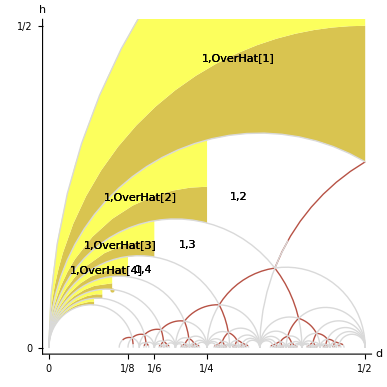

```mathematica
Ch3SpiralExample
```

```mathematica
viSpirals2 :=  Module[{kList},
kList = {2,3,4};

Show[
spiralBackground,
Graphics[Map[viTwoLattice,kList]]
,PlotRange->{{0,0.5},{0,0.5}}
,Ticks -> {{0,1/8,1/6,1/4,1/2},{0,1/2}}
,Axes->True,BaseStyle->setGill
,AxesLabel-> {"d","h"}
]
];

viSpirals3 :=  Module[{kList},
kList = {2,3,4};

Show[
spiralBackground,
Graphics[Map[viThreeLattice,kList]]
]
];
viTwoLattice[k_] := Module[{d,hd,labels,lpn},
d = Mean@{1/(2(k+1)),1/(2k)};
(*hd = Echo@dhColumnTwo[d,k];
*)
hd1 = {{0.3,0.45},{0.3,0.234},{0.145,0.234},{0.22,0.1597},{0.1125,0.1597}
,{0.15,0.12},{0.09,0.12}};

labels = Map[ Text[ twoLabel[#],#,Background->White]&,hd1];
{
(*{Gray,
Map[ InfiniteLine[{{1/(2#),0},{1/(2#),1}}]&,{k}]
,Map[ InfiniteLine[{{1/(2(#+1)),0},{1/(2(#+1)),1}}]&,{k}]
},
*)labels
}
];
viThreeLattice[k_] := Module[{d,hd,labels,lpn},
d = Mean@{1/(2(k+1)),1/(2k)};
hd = dhColumn[d,k];

labels = Map[ Text[ threeLabel[#],#]&,hd];
{
{Gray,
Map[ InfiniteLine[{{1/(2#),0},{1/(2#),1}}]&,{k}]
,Map[ InfiniteLine[{{1/(2(#+1)),0},{1/(2(#+1)),1}}]&,{k}]
}
,labels
}
];

viAndLattice[{d_, h_},kList_] := Module[{slattice,lpn},
slattice =  latticeCreateDH[{d,h},{0,2}];
lpn = latticeParastichyNumbers[slattice];
hats = Map[hatName,lpn];
label = GraphicsRow[Map[Graphics[Text[#]]&,hats],AspectRatio->3];

GraphicsRow[{
viPosition[{d,h},kList]
,ch4showParastichyLines[slattice]
,label
}]
];

dhColumn[d_,k_] := Module[{hList,dhList},
hList =Map[ Last@hdofTransition[d,#]&,{0,1,2,3}];
hList = Select[hList ,Im[#]==0&];
hList = Reverse@Sort@Join[hList*1.1,hList*0.9];
dhList = Map[{d,#}&,hList];
dhList
];
dhColumnTwo[d_,k_] := Module[{hList,dhList},
hList =Map[ Last@hdofTransition[d,#]&,{0,1,2,3}];
hList = Select[hList ,Im[#]==0&];
hList = MovingAverage[hList,2];
hList = Reverse@Sort@hList;
dhList = Map[{d,#}&,hList];
dhList
];


viPosition[pt_,kList_] := Module[{hdList},
Show[
spiralBackground,Graphics[{
{Gray,
Map[ InfiniteLine[{{1/(2#),0},{1/(2#),1}}]&,kList]
,Map[ InfiniteLine[{{1/(2(#+1)),0},{1/(2(#+1)),1}}]&,kList]
}
, Map[hatTransition,{0,1,2,3}]
,Red,Point[pt]}]]
];
hatName[n_] := Style[ToString[n],setGill];
hatName[hat[n_]] := DisplayForm[OverHat[hatName[n]]]
```